```mathematica
Clear["Global`*"]
```

## Hide

```mathematica
A0 = π r0^2;
A[t_]=π r[t]^2;
(*CD=32±0.26 MSH/day*)
DSolve[A'[t]==-1/w r[t]/r0,r[t],t]
```

{{r[t]→0},{r[t]→-t/(2 π r0 w)+C[1]}}

```mathematica
Solve[0==π(r0-t/(2 π r0 w))^2,t]
```

{{t→2 π r0^2 w},{t→2 π r0^2 w}}

```mathematica
(2 π r0^2)/CD
```

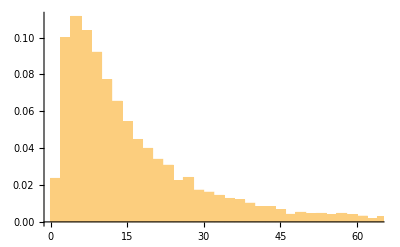

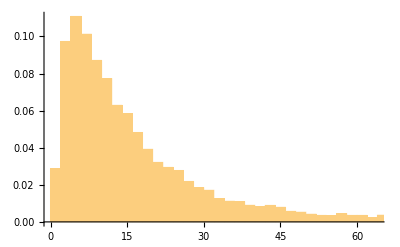

```mathematica
μ=11.8; σ=2.55;Histogram[Exp[RandomVariate[NormalDistribution[Log[μ],Log[σ]],10000]],Automatic,"Probability"]
Histogram[RandomVariate[LogNormalDistribution[Log[μ],Log[σ]],10000],Automatic,"Probability"]
```

```mathematica
(*what Ari uses*)e^NormalDistribution[Log[μ],Log[σ]]==LogNormalDistribution[Log[μ],Log[σ]]
```

```mathematica
A[t_]=Expand[(√A0-d/(√A0)t)^2]
```

A0-2 d t+(d^2 t^2)/A0

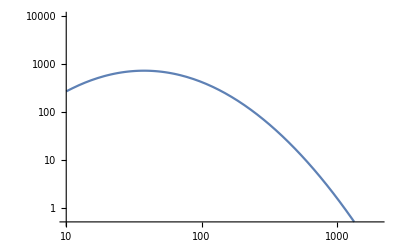

```mathematica
μ=Log[90.24]; σ=Log[2.55];
LogLogPlot[100000 Exp[-(Log[x]-μ)^2/(2 σ^2)]/(x σ √(2 π)),{x,10,2000}, PlotRange->{.5,10000}]
```

```mathematica
1.54*58.6
1.54*30.2
```

90.244

46.508

```mathematica
15203./(15203+34562)
```

0.305496

```mathematica
NSolve[Simplify[D[test,a]==0],a, Reals]
```

{{a→58.133}}

500000 (-(0.274705 ⅇ^(-4.95861-0.548076 (-4.50247+Log[a])^2) (-4.50247+Log[a]))/a-(0.240469 ⅇ^(-4.22007-0.657198 (-3.83967+Log[a])^2) (-3.83967+Log[a]))/a)

```mathematica
Chop[Integrate[Exp[-(Log[x]-μ)^2/(2 σ^2)]/(x σ √(2 π)), {x,0, ∞}]]
```

1.

```mathematica
(*LOGNORMAL MEAN!*)
Simplify[Integrate[x Exp[-(Log[x]-μ)^2/(2 σ^2)]/(x σ √(2 π)), {x,0, ∞}]]
lognmean==ⅇ^(μ+σ^2/2)
Log[lognmean]-σ^2/2==μ
```

ConditionalExpression[ⅇ^(μ+σ^2/2) √(1/σ^2) σ,Re[σ^2]>0]

lognmean==ⅇ^(μ+σ^2/2)

-σ^2/2+Log[lognmean]==μ

```mathematica
(*LOGNORMAL MEDIAN!*)
Simplify[Integrate[Exp[-(Log[x]-μ)^2/(2 σ^2)]/(x σ √(2 π)), {x,0, m}]]==1/2
```

ConditionalExpression[1/2 (√(1/σ^2) σ-Erf[(μ-Log[m])/(√2 σ)])==1/2,Re[σ^2]>0||(Re[σ^2]≥0&&Re[μ/σ^2]>0)]

```mathematica
Erf[(μ-Log[m])/(√2 σ)]==0
(μ-Log[m])/(√2 σ)==0
Log[lognmedian]==μ
lognmedian==e^μ
```

Erf[(μ-Log[m])/(√2 σ)]==0

(μ-Log[m])/(√2 σ)==0

Log[lognmedian]==μ

lognmedian==e^μ

```mathematica
(*LOGNORMAL SIGMA!*)
ⅇ^(μ+σ^2/2)==lognmean
lognmedian ⅇ^(σ^2/2)==lognmean
σ==√(2 Log[lognmean/lognmedian])
```

ⅇ^(μ+σ^2/2)==lognmean

ⅇ^(σ^2/2) lognmedian==lognmean

σ==√2 √Log[lognmean/lognmedian]

```mathematica
SD^2==(Exp[σ^2]-1)Exp[2μ+σ^2]
```

SD^2==ⅇ^(2 μ+σ^2) (-1+ⅇ^(σ^2))

## MSH conversion

```mathematica
(*https://arxiv.org/pdf/1409.4337.pdf*)
m = 1/1000km;
arcsecond = π/(180*3600)149597870700m;
N[arcsecond];
(5.8arcsecond)^2
3.04*^13/10 m^2
```

1.76952×10^7 km^2

3.04×10^6 km^2

```mathematica
(*https://www.sizes.com/units/microhemisphere.htm*)
600000 miles^2*(1.6 km/miles)^2(*square meters in a MSH*)
π *(4200/2 km)^2/4.5
```

1.536×10^6 km^2

3.07876×10^6 km^2

```mathematica
(*my guess*)
a=Simplify[4 π (696000km)^2/2/1000000]
Simplify[√a/(696000.0  km/(R☉))]
a=Simplify[4 π (R☉)^2/2/1000000]
Simplify[√N[a]]
```

968832 km^2 π

```mathematica
(0.002506628274631 5 √(km^2) R☉)/km
```

(π (R☉)^2)/500000

0.00250663 √((R☉)^2)

```mathematica
√(2.*^-6 π)
```

0.00250663

```mathematica
(*Ari's code*)
√(17682025(*(725*5.8)^2*))km
√(17682025(*(725*5.8)^2*))/696000.0
```

4205000 m

0.00604167

```mathematica
(√(17682025(*(725*5.8)^2*))/696000.0)/(√(2.*^-6 π))
```

2.41028

## CDF inversion 1

```mathematica
normal = 1/(√(2 π)σ)Exp[-(x-μ)^2/(2 σ^2)];
lognormal= 1/(x √(2 π)σ)Exp[(-(Log[x]-Log[μ])^2)/(2 σ^2)];
1/2 +Integrate[normal,x];
1/2 +Integrate[lognormal,x];
```

```mathematica
func = Exp[-(Log[a]-Log[mean])^2/(2 Log[σa])];
func=Simplify[Normal[func/Integrate[func,{a,0,∞}]]]
```

(ⅇ^(-(Log[a]-Log[mean])^2/(2 Log[σa])))/(mean √(2 π) √σa √Log[σa])

```mathematica
test=Simplify[(func/.{σa->Exp[σ^2],a->x,mean->μ})]
1/2 +Integrate[test,x]
(*1/2 +Integrate[func,a]*)
```

(ⅇ^(-(Log[x]-Log[μ])^2/(2 Log[ⅇ^(σ^2)])))/(√(ⅇ^(σ^2)) √(2 π) μ √Log[ⅇ^(σ^2)])

1/2-1/2 Erf[(Log[ⅇ^(σ^2)]-Log[x]+Log[μ])/(√2 √Log[ⅇ^(σ^2)])]

```mathematica
z=((Log[x]-Log[μ])/σ-σ);
U==1/2+1/2 Erf[1/(√2)z]
μ Exp[σ(√2 InverseErf[2 U-1]+σ)]==x
μ (Exp[σ]Exp[√2 InverseErf[2 U-1]])^σ==x
μ (Exp[σ]draws)^σ==x
```

U==1/2+1/2 Erf[(-σ+(Log[x]-Log[μ])/σ)/(√2)]

ⅇ^(σ (σ+√2 InverseErf[-1+2 U])) μ==x

(ⅇ^(σ+√2 InverseErf[-1+2 U]))^σ μ==x

(draws ⅇ^σ)^σ μ==x

## CDF inversion 2

```mathematica
lt=1/(d √(2 π)σlogD)Exp[(-(Log[d]-μlogD)^2)/(2 σlogD^2)];
test=Simplify[(lt/.{σlogD->σ,d->x,μlogD->Log[μ]})];
1/2 +Integrate[test,x]
(*1/2 +Integrate[func,a]*)
```

1/2+1/2 Erf[(Log[x]-Log[μ])/(√2 σ)]

```mathematica
z=((Log[x]-Log[μ])/σ)
U==1/2+1/2 Erf[1/(√2)z]
μ (Exp[√2 InverseErf[2U-1]])^σ==x
μ draws^σ==x
```

(Log[x]-Log[μ])/σ

U==1/2+1/2 Erf[(Log[x]-Log[μ])/(√2 σ)]

(ⅇ^(√2 InverseErf[-1+2 U]))^σ μ==x

draws^σ μ==x

## plot matching

```mathematica
(*weird lognormal from Baumann 2005, eq. 2*)
func = Exp[-(Log[a]-Log[mean])^2/(2 Log[σa])];
func=Simplify[Normal[func/Integrate[func,{a,0,∞}]]]
```

(ⅇ^(-(Log[a]-Log[mean])^2/(2 Log[σa])))/(mean √(2 π) √σa √Log[σa])

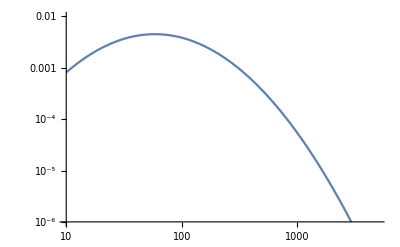

```mathematica
(*spot groups, looking at dashed line, fig 2 https://arxiv.org/pdf/astro-ph/0510516.pdf Baumann 2005*)
test = (func/.{mean->90.24/1.54, σa->2.49});
LogLogPlot[test,{a,10,5000}, PlotRange->{10^-6,10^-2}]
```

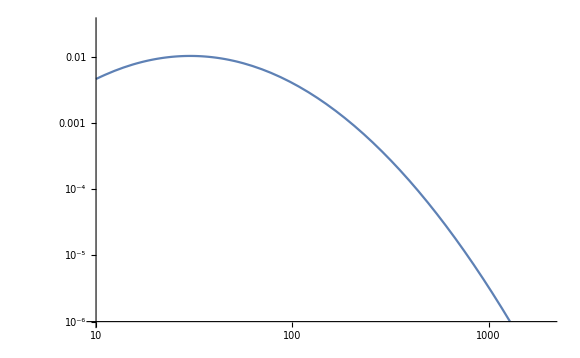

```mathematica
(*single spots, looking at dashed line, fig 3*)
test = (func/.{mean->30.2(*46.51/1.54*), σa->2.14});
LogLogPlot[test,{a,10,2000}, PlotRange->{10^-6,10^-1.5}]
```

200000 (0.00175994 ⅇ^(-0.548076 (-4.50247+Log[a])^2)+0.00268893 ⅇ^(-0.657198 (-3.83967+Log[a])^2))

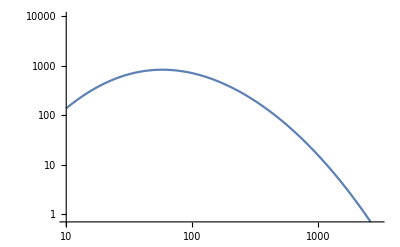

```mathematica
(*all spots and groups, fig 2 https://arxiv.org/pdf/1505.07361.pdf Borgniet 2015*)
test =200000 (0.4*(func/.{mean->46.51, σa->2.14})+0.6* (func/.{mean->90.24, σa->2.49}))
LogLogPlot[test,{a,10,3000}, PlotRange->{0.7,10000}]
```

```mathematica
(*lognormal from Pillet 1993, eq. 5?, http://adsabs.harvard.edu/abs/1993A%26A...274..521M*)
lt = 1/(d √(2 π)σlogD)Exp[(-(Log[d]-μlogD)^2)/(2 σlogD^2)];
(*lt = Log[d]/(√(2 π)σlogD)Exp[(-(Log[d]-μlogD)^2)/(2 σlogD^2)];*)
```

2.69463

2.619

0.699335

0.806

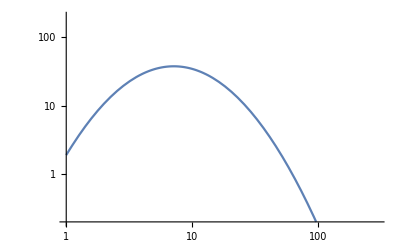

```mathematica
(*individual spots, fig 2b Pillet 1993*)
Log[14.8]
2.619
√(2Log[18.9/14.8])
0.806
test =2*375*lt/.{μlogD->2.619, σlogD->0.806};
LogLogPlot[test,{d,1,300}, PlotRange->{0.2, 200}]
```

3.43076

3.373

0.761717

0.869

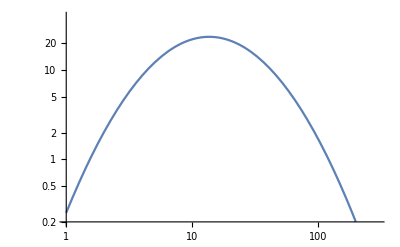

```mathematica
(*spot groups, fig 1b Pillet 1993*)
Log[30.9]
3.373
√(2Log[41.3/30.9])
0.869
test =2*515*lt/.{μlogD->3.373, σlogD->0.869};
LogLogPlot[test,{d,1,300}, PlotRange->{0.2, 40}]
```

## paper plots

```mathematica
Plot[v[t,0.5,1],{t,0,3}, BaseStyle->{FontWeight->"Bold",FontSize->36}, PlotStyle->{Thickness->.01},Frame->True, FrameLabel->{"Time (years)","Radial velocity (cm/s)"}]
```

```mathematica
(*weird lognormal from Baumann 2005, eq. 2*)
func = Exp[-(Log[a]-Log[mean])^2/(2 Log[σa])];
func=Simplify[Normal[func/Integrate[func,{a,0,∞}]]]
```

(ⅇ^(-(Log[a]-Log[mean])^2/(2 Log[σa])))/(mean √(2 π) √σa √Log[σa])

```mathematica
(*spot groups, looking at dashed line, fig 2 https://arxiv.org/pdf/astro-ph/0510516.pdf Baumann 2005*)
test1 = (func/.{mean->90.24/1.54, σa->2.49});
LogLogPlot[test1,{a,10,5000}, PlotRange->{10^-6,10^-2},BaseStyle->{FontWeight->"Bold",FontSize->20}, PlotStyle->{Thickness->.01},Frame->True, FrameLabel->{"Maximum Area (MSH)","Number Density"}];
```

```mathematica
(*single spots, looking at dashed line, fig 3*)
test2 = (func/.{mean->30.2(*46.51/1.54*), σa->2.14});
LogLogPlot[test2,{a,10,2000}, PlotRange->{10^-6,10^-1.5},BaseStyle->{FontWeight->"Bold",FontSize->20}, PlotStyle->{Thickness->.01},Frame->True, FrameLabel->{"Maximum Area (MSH)","Number Density"}];
```

```mathematica
(*all spots and groups, fig 2 https://arxiv.org/pdf/1505.07361.pdf Borgniet 2015*)
test3 =0.4*(func/.{mean->46.51, σa->2.14})+0.6* (func/.{mean->90.24, σa->2.49});
LogLogPlot[test3,{a,10,3000}, PlotRange->Automatic,BaseStyle->{FontWeight->"Bold",FontSize->20}, PlotStyle->{Thickness->.01},Frame->True, FrameLabel->{"Maximum Area (MSH)","Number Density"}];
```

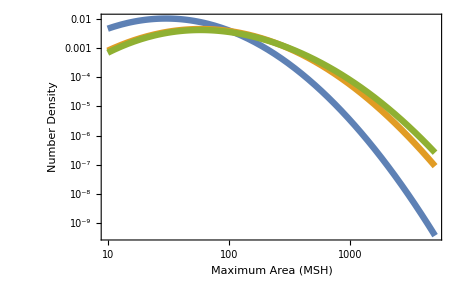

```mathematica
LogLogPlot[{test2,test1,test3},{a,10,5000}, PlotRange->Automatic,BaseStyle->{FontWeight->"Bold",FontSize->20}, PlotStyle->{Thickness->.01},Frame->True, FrameLabel->{"Maximum Area (MSH)","Number Density"}]
```

```mathematica
(*lognormal from Pillet 1993, eq. 5?, http://adsabs.harvard.edu/abs/1993A%26A...274..521M*)
lt = 1/(d √(2 π)σlogD)Exp[(-(Log[d]-μlogD)^2)/(2 σlogD^2)];
(*lt = Log[d]/(√(2 π)σlogD)Exp[(-(Log[d]-μlogD)^2)/(2 σlogD^2)];*)
```

```mathematica
(*individual spots, fig 2b Pillet 1993*)
test4 =lt/.{μlogD->2.619, σlogD->0.806};
LogLogPlot[test,{d,1,300}, PlotRange->{0.2, 200}];
```

```mathematica
(*spot groups, fig 1b Pillet 1993*)
test5 =lt/.{μlogD->3.373, σlogD->0.869};
LogLogPlot[test,{d,1,300}, PlotRange->{0.2, 40}];
```

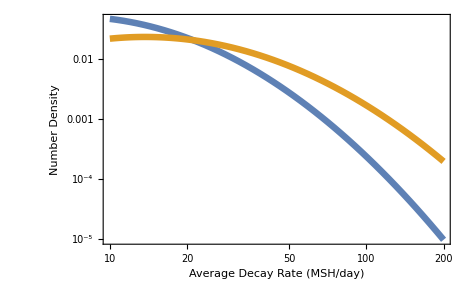

```mathematica
LogLogPlot[{test4,test5},{d,10,200}, PlotRange->Automatic,BaseStyle->{FontWeight->"Bold",FontSize->20}, PlotStyle->{Thickness->.01},Frame->True, FrameLabel->{"Average Decay Rate (MSH/day)","Number Density"}]
```